```mathematica
SetDirectory["/Users/paul/univ/eratosthenes/results/formatted/"]
benchLaptopPut = Import["out-dist2proc.264449"];
```

/Users/paul/univ/eratosthenes/results/formatted

```mathematica
fit = Fit[benchLaptopPut, {1,x},{x}]
fitPlot=Plot[fit,{x,0,250}];
```

15714.2+100.501 x

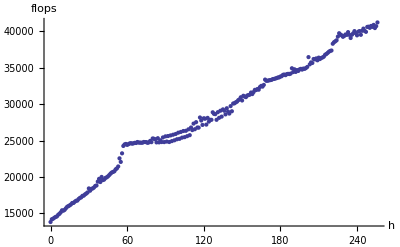

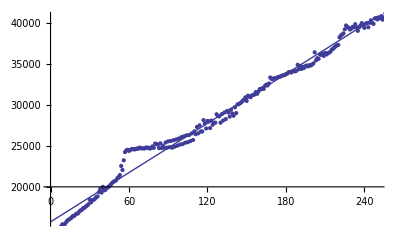

bench-huy-put-p2-dist.png

```mathematica
benchlaptopput=ListPlot[benchLaptopPut, AxesLabel->{"h", "flops"}]
both=Show[{fitPlot, benchlaptopput}]
Export["bench-huy-put-p2-dist.png", both]
```